```mathematica
FEt[pa_,pb_]:=Module[{n,n1,n2,ft,A,ev,i},n=40;
ft=0.0;
For[n1=0,n1<n,n1++,For[n2=0,n2<n,n2++,A={{-2 V pa,-1-Exp[I 2 Pi n2/n],-1-Exp[-I 2 Pi n1/n]},{-1-Exp[-I 2 Pi n2/n],-2 V pb,-1-Exp[-I 2 Pi n1/n] Exp[-I 2 Pi n2/n]},{-1-Exp[I 2 Pi n1/n],-1-Exp[I 2 Pi n1/n] Exp[I 2 Pi n2/n],2 V (pa+pb)}};
ev=Eigenvalues[A];
For[i=1,i<=3,i++,ft+=-T Log[1+Exp[-(ev[[i]]-mu)/T]]/n^2];];];
ft]
```

```mathematica
AbsoluteTiming[FEt[0.2,0.1]]
```

{0.0177106,-3.33137}

```mathematica
test=FEt[0.2,0.1];
{Head[test],NumericQ[test]}
```

{Plus,False}

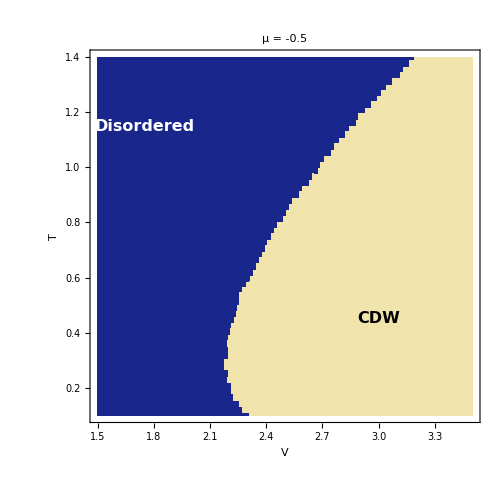

```mathematica
muFixed=-0.5;

Tmin=0.1;Tmax=1.4;nT=60;

VbisMin=1.5;VbisMax=3.5;nbis=10;
Vplotmin=1.5;Vplotmax=3.5;nV=120;

del=10^-6;mit=40;
ordCut=10^-3;

(*---Step 1:critical line Vc(T) by bisection at fixed mu---*)
For[iT=0,iT<=nT,iT++,T=Tmin+iT/nT (Tmax-Tmin);
mu=muFixed;
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;
pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
f00=FEt[pa,pb];
fa=FEt[pa+del,pb];
fb=FEt[pa,pb+del];
dfta=(fa-f00)/del; 
dftb=(fb-f00)/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
ord=Sqrt[pa^2+pb^2+(pa+pb)^2];
crit=If[ord>ordCut,1,0];
If[crit==1,v2=V,v1=V];];
tVal[iT]=T;
Vc[iT]=(v1+v2)/2;];

(*---Step 2:explicit arrays---*)
tVals=Table[tVal[i],{i,0,nT}];
vcVals=Table[Vc[i],{i,0,nT}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Step 3:phase map with axes x=V,y=T---*)
phasePlotVT4=Flatten[Table[{vVals[[j+1]],tVals[[i+1]],If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nT},{j,0,nV}],1];

critLineT=Table[{tVals[[i+1]],vcVals[[i+1]]},{i,0,nT}];
smooth=Interpolation[critLineT,InterpolationOrder->3];

tFine=Table[Tmin+s/400. (Tmax-Tmin),{s,0,400}];
smoothLine=Table[{smooth[t],t},{t,tFine}];

ListDensityPlot[phasePlotVT4,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],RGBColor[0.10,0.15,0.55]]&),Frame->True,PlotLabel->"μ = -0.5",FrameLabel->{Style["V",15],Rotate[Style["T",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Tmin,Tmax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{3.0,0.45}],Text[Style["Disordered",16,Bold,White],{1.75,1.15}]}]
```

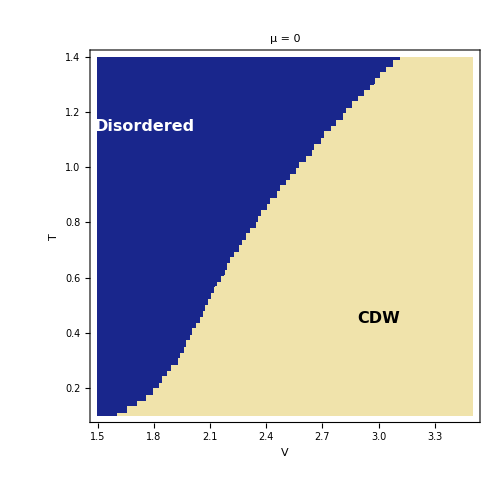

```mathematica
muFixed=0;

Tmin=0.1;Tmax=1.4;nT=60;

VbisMin=1.5;VbisMax=3.5;nbis=10;
Vplotmin=1.5;Vplotmax=3.5;nV=120;

del=10^-6;mit=40;
ordCut=10^-3;

(*---Step 1:critical line Vc(T) by bisection at fixed mu---*)
For[iT=0,iT<=nT,iT++,T=Tmin+iT/nT (Tmax-Tmin);
mu=muFixed;
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;
pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
f00=FEt[pa,pb];
fa=FEt[pa+del,pb];
fb=FEt[pa,pb+del];
dfta=(fa-f00)/del; 
dftb=(fb-f00)/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
ord=Sqrt[pa^2+pb^2+(pa+pb)^2];
crit=If[ord>ordCut,1,0];
If[crit==1,v2=V,v1=V];];
tVal[iT]=T;
Vc[iT]=(v1+v2)/2;];

(*---Step 2:explicit arrays---*)
tVals=Table[tVal[i],{i,0,nT}];
vcVals=Table[Vc[i],{i,0,nT}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Step 3:phase map with axes x=V,y=T---*)
phasePlotVT4=Flatten[Table[{vVals[[j+1]],tVals[[i+1]],If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nT},{j,0,nV}],1];

critLineT=Table[{tVals[[i+1]],vcVals[[i+1]]},{i,0,nT}];


tFine=Table[Tmin+s/400. (Tmax-Tmin),{s,0,400}];


ListDensityPlot[phasePlotVT4,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],RGBColor[0.10,0.15,0.55]]&),Frame->True,PlotLabel->"μ = 0",FrameLabel->{Style["V",15],Rotate[Style["T",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Tmin,Tmax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{3.0,0.45}],Text[Style["Disordered",16,Bold,White],{1.75,1.15}]}]
```

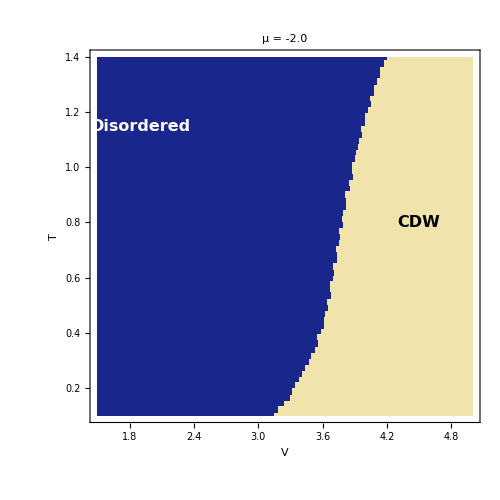

```mathematica
muFixed=-2.0;

Tmin=0.1;Tmax=1.4;nT=60;

VbisMin=1.5;VbisMax=5.0;nbis=10;
Vplotmin=1.5;Vplotmax=5.0;nV=120;

del=10^-6;mit=40;
ordCut=10^-3;

(*---Step 1:critical line Vc(T) by bisection at fixed mu---*)
For[iT=0,iT<=nT,iT++,T=Tmin+iT/nT (Tmax-Tmin);
mu=muFixed;
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;
pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
f00=FEt[pa,pb];
fa=FEt[pa+del,pb];
fb=FEt[pa,pb+del];
dfta=(fa-f00)/del; 
dftb=(fb-f00)/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
ord=Sqrt[pa^2+pb^2+(pa+pb)^2];
crit=If[ord>ordCut,1,0];
If[crit==1,v2=V,v1=V];];
tVal[iT]=T;
Vc[iT]=(v1+v2)/2;];

(*---Step 2:explicit arrays---*)
tVals=Table[tVal[i],{i,0,nT}];
vcVals=Table[Vc[i],{i,0,nT}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Step 3:phase map with axes x=V,y=T---*)
phasePlotVT4=Flatten[Table[{vVals[[j+1]],tVals[[i+1]],If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nT},{j,0,nV}],1];

critLineT=Table[{tVals[[i+1]],vcVals[[i+1]]},{i,0,nT}];


tFine=Table[Tmin+s/400. (Tmax-Tmin),{s,0,400}];


ListDensityPlot[phasePlotVT4,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],RGBColor[0.10,0.15,0.55]]&),Frame->True,PlotLabel->"μ = -2.0",FrameLabel->{Style["V",15],Rotate[Style["T",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Tmin,Tmax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{4.5,0.8}],Text[Style["Disordered",16,Bold,White],{1.9,1.15}]}]
```

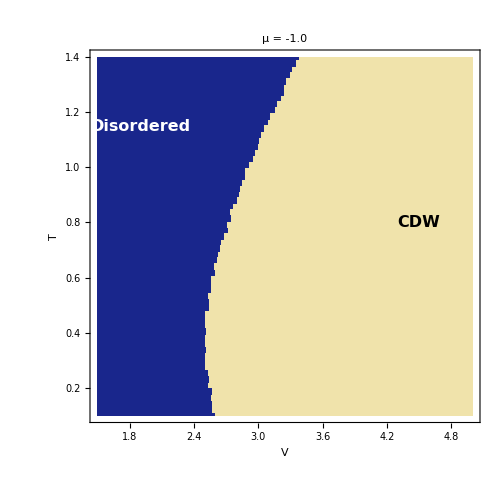

```mathematica
muFixed=-1.0;

Tmin=0.1;Tmax=1.4;nT=60;

VbisMin=1.5;VbisMax=5.0;nbis=10;
Vplotmin=1.5;Vplotmax=5.0;nV=120;

del=10^-6;mit=40;
ordCut=10^-3;

(*---Step 1:critical line Vc(T) by bisection at fixed mu---*)
For[iT=0,iT<=nT,iT++,T=Tmin+iT/nT (Tmax-Tmin);
mu=muFixed;
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;
pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
f00=FEt[pa,pb];
fa=FEt[pa+del,pb];
fb=FEt[pa,pb+del];
dfta=(fa-f00)/del; 
dftb=(fb-f00)/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
ord=Sqrt[pa^2+pb^2+(pa+pb)^2];
crit=If[ord>ordCut,1,0];
If[crit==1,v2=V,v1=V];];
tVal[iT]=T;
Vc[iT]=(v1+v2)/2;];

(*---Step 2:explicit arrays---*)
tVals=Table[tVal[i],{i,0,nT}];
vcVals=Table[Vc[i],{i,0,nT}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Step 3:phase map with axes x=V,y=T---*)
phasePlotVT4=Flatten[Table[{vVals[[j+1]],tVals[[i+1]],If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nT},{j,0,nV}],1];

critLineT=Table[{tVals[[i+1]],vcVals[[i+1]]},{i,0,nT}];


tFine=Table[Tmin+s/400. (Tmax-Tmin),{s,0,400}];


ListDensityPlot[phasePlotVT4,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],RGBColor[0.10,0.15,0.55]]&),Frame->True,PlotLabel->"μ = -1.0",FrameLabel->{Style["V",15],Rotate[Style["T",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Tmin,Tmax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{4.5,0.8}],Text[Style["Disordered",16,Bold,White],{1.9,1.15}]}]
```

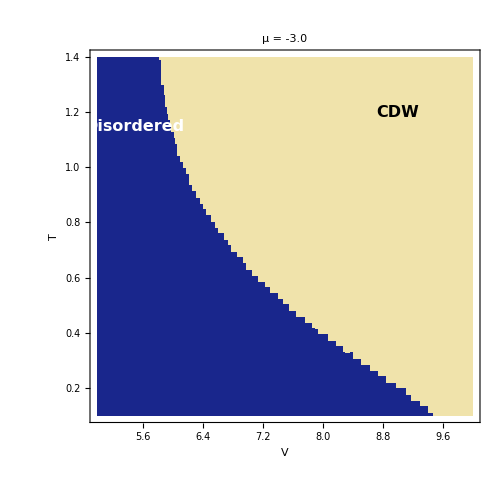

```mathematica
muFixed=-3.0;

Tmin=0.1;Tmax=1.4;nT=60;

VbisMin=5.0;VbisMax=10.0;nbis=10;
Vplotmin=5.0;Vplotmax=10.0;nV=120;

del=10^-6;mit=40;
ordCut=10^-3;

(*---Step 1:critical line Vc(T) by bisection at fixed mu---*)
For[iT=0,iT<=nT,iT++,T=Tmin+iT/nT (Tmax-Tmin);
mu=muFixed;
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;
pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
f00=FEt[pa,pb];
fa=FEt[pa+del,pb];
fb=FEt[pa,pb+del];
dfta=(fa-f00)/del; 
dftb=(fb-f00)/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
ord=Sqrt[pa^2+pb^2+(pa+pb)^2];
crit=If[ord>ordCut,1,0];
If[crit==1,v2=V,v1=V];];
tVal[iT]=T;
Vc[iT]=(v1+v2)/2;];

(*---Step 2:explicit arrays---*)
tVals=Table[tVal[i],{i,0,nT}];
vcVals=Table[Vc[i],{i,0,nT}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Step 3:phase map with axes x=V,y=T---*)
phasePlotVT4=Flatten[Table[{vVals[[j+1]],tVals[[i+1]],If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nT},{j,0,nV}],1];

critLineT=Table[{tVals[[i+1]],vcVals[[i+1]]},{i,0,nT}];


tFine=Table[Tmin+s/400. (Tmax-Tmin),{s,0,400}];


ListDensityPlot[phasePlotVT4,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],RGBColor[0.10,0.15,0.55]]&),Frame->True,PlotLabel->"μ = -3.0",FrameLabel->{Style["V",15],Rotate[Style["T",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Tmin,Tmax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{9,1.2}],Text[Style["Disordered",16,Bold,White],{5.5,1.15}]}]
```

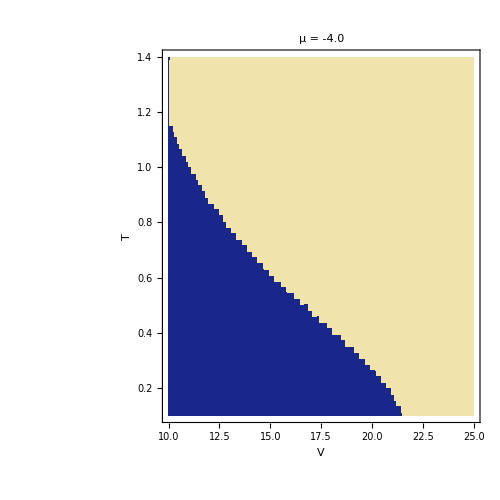

```mathematica
muFixed=-4.0;

Tmin=0.1;Tmax=1.4;nT=60;

VbisMin=10.0;VbisMax=25.0;nbis=10;
Vplotmin=10.0;Vplotmax=25.0;nV=120;

del=10^-6;mit=40;
ordCut=10^-3;

(*---Step 1:critical line Vc(T) by bisection at fixed mu---*)
For[iT=0,iT<=nT,iT++,T=Tmin+iT/nT (Tmax-Tmin);
mu=muFixed;
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;
pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
f00=FEt[pa,pb];
fa=FEt[pa+del,pb];
fb=FEt[pa,pb+del];
dfta=(fa-f00)/del; 
dftb=(fb-f00)/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
ord=Sqrt[pa^2+pb^2+(pa+pb)^2];
crit=If[ord>ordCut,1,0];
If[crit==1,v2=V,v1=V];];
tVal[iT]=T;
Vc[iT]=(v1+v2)/2;];

(*---Step 2:explicit arrays---*)
tVals=Table[tVal[i],{i,0,nT}];
vcVals=Table[Vc[i],{i,0,nT}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Step 3:phase map with axes x=V,y=T---*)
phasePlotVT4=Flatten[Table[{vVals[[j+1]],tVals[[i+1]],If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nT},{j,0,nV}],1];

critLineT=Table[{tVals[[i+1]],vcVals[[i+1]]},{i,0,nT}];


tFine=Table[Tmin+s/400. (Tmax-Tmin),{s,0,400}];


ListDensityPlot[phasePlotVT4,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],RGBColor[0.10,0.15,0.55]]&),Frame->True,PlotLabel->"μ = -4.0",FrameLabel->{Style["V",15],Rotate[Style["T",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Tmin,Tmax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{9,1.2}],Text[Style["Disordered",16,Bold,White],{5.5,1.15}]}]
```

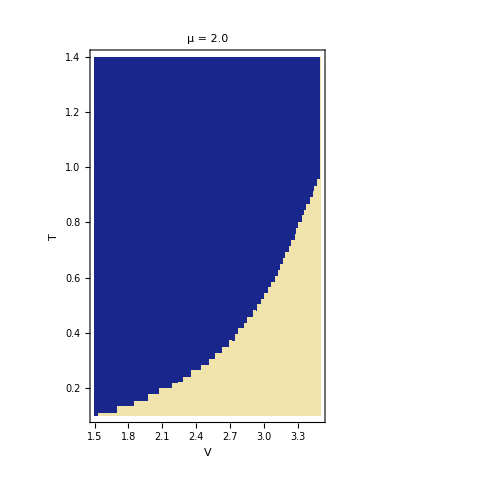

```mathematica
muFixed=2.0;

Tmin=0.1;Tmax=1.4;nT=60;

VbisMin=1.5;VbisMax=3.5;nbis=10;
Vplotmin=1.5;Vplotmax=3.5;nV=120;

del=10^-6;mit=40;
ordCut=10^-3;

(*---Step 1:critical line Vc(T) by bisection at fixed mu---*)
For[iT=0,iT<=nT,iT++,T=Tmin+iT/nT (Tmax-Tmin);
mu=muFixed;
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;
pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
f00=FEt[pa,pb];
fa=FEt[pa+del,pb];
fb=FEt[pa,pb+del];
dfta=(fa-f00)/del; 
dftb=(fb-f00)/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
ord=Sqrt[pa^2+pb^2+(pa+pb)^2];
crit=If[ord>ordCut,1,0];
If[crit==1,v2=V,v1=V];];
tVal[iT]=T;
Vc[iT]=(v1+v2)/2;];

(*---Step 2:explicit arrays---*)
tVals=Table[tVal[i],{i,0,nT}];
vcVals=Table[Vc[i],{i,0,nT}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Step 3:phase map with axes x=V,y=T---*)
phasePlotVT5=Flatten[Table[{vVals[[j+1]],tVals[[i+1]],If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nT},{j,0,nV}],1];

critLineT=Table[{tVals[[i+1]],vcVals[[i+1]]},{i,0,nT}];


tFine=Table[Tmin+s/400. (Tmax-Tmin),{s,0,400}];


ListDensityPlot[phasePlotVT5,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],RGBColor[0.10,0.15,0.55]]&),Frame->True,PlotLabel->"μ = 2.0",FrameLabel->{Style["V",15],Rotate[Style["T",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Tmin,Tmax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{9,1.2}],Text[Style["Disordered",16,Bold,White],{5.5,1.15}]}]
```

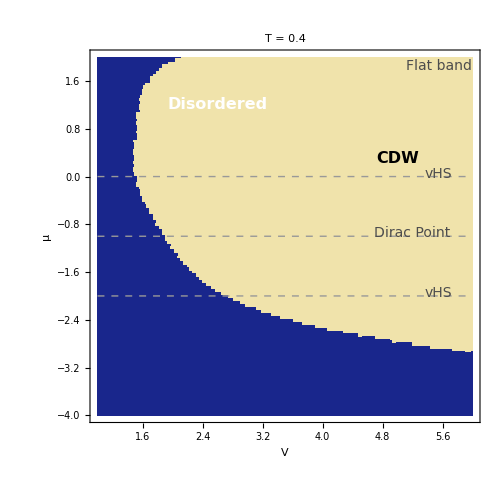

```mathematica
(* =========================*)(*mu-V phase diagram*)(*fixed T*)(* =========================*)
TFixed=0.4;   (*change to 0.6,1.0,etc.*)

muMin=-4.0;muMax=2.0;nMu=120;
VMin=1.0;VMax=6.0;nV=120;

del=10^-6;
mit=10;
ordCut=10^-3;

(*----build explicit grids----*)
muVals=Table[muMin+i/nMu (muMax-muMin),{i,0,nMu}];
vVals=Table[VMin+j/nV (VMax-VMin),{j,0,nV}];

(*----fixed temperature----*)
T=TFixed;

(*----phase map on (V,mu) grid----*)
phasePlotMuV=Flatten[Table[mu=muVals[[i+1]];
V=vVals[[j+1]];
pa=0.05;
pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
f00=FEt[pa,pb];
fa=FEt[pa+del,pb];
fb=FEt[pa,pb+del];
dfta=(fa-f00)/del;
dftb=(fb-f00)/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
ord=Sqrt[pa^2+pb^2+(pa+pb)^2];
crit=If[ord>ordCut,1,0];
{V,mu,crit},{i,0,nMu},{j,0,nV}],1];

(*----plot----*)
ListDensityPlot[phasePlotMuV,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],(*CDW*)RGBColor[0.10,0.15,0.55]    (*Disordered*)]&),Frame->True,PlotLabel->Row[{"T = ",NumberForm[TFixed,{3,1}]}],FrameLabel->{Style["V",15],Rotate[Style["μ",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{VMin,VMax},{muMin,muMax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{5.0,0.3}],Text[Style["Disordered",16,Bold,White],{2.6,1.2}],Dashed,GrayLevel[0.6],Line[{{VMin,0.0},{VMax,0.0}}],Line[{{VMin,-1.0},{VMax,-1.0}}],Line[{{VMin,-2.0},{VMax,-2.0}}],Text[Style["vHS",14,GrayLevel[0.3]],{5.55,0.05}],Text[Style["Dirac Point",14,GrayLevel[0.3]],{5.2,-0.95}],Text[Style["vHS",14,GrayLevel[0.3]],{5.55,-1.95}],Text[Style["Flat band",14,GrayLevel[0.3]],{5.55,1.85}]}]
```

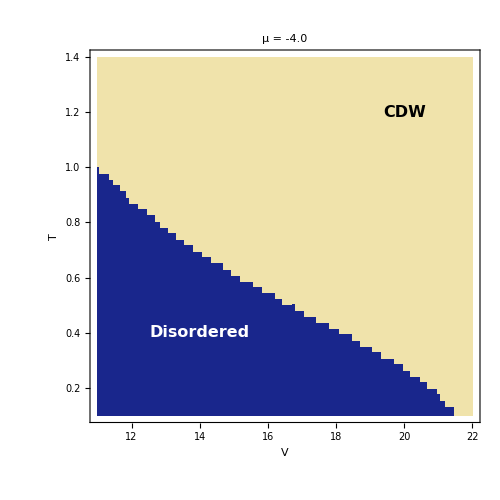

```mathematica
ListDensityPlot[phasePlotVT4,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],RGBColor[0.10,0.15,0.55]]&),Frame->True,PlotLabel->"μ = -4.0",FrameLabel->{Style["V",15],Rotate[Style["T",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{11,22},{Tmin,Tmax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{20,1.2}],Text[Style["Disordered",16,Bold,White],{14,0.4}]}]
```

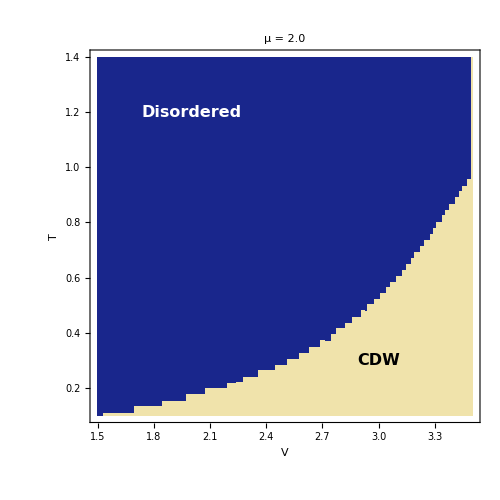

```mathematica
ListDensityPlot[phasePlotVT5,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],RGBColor[0.10,0.15,0.55]]&),Frame->True,PlotLabel->"μ = 2.0",FrameLabel->{Style["V",15],Rotate[Style["T",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Tmin,Tmax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{3.0,0.3}],Text[Style["Disordered",16,Bold,White],{2.0,1.2}]}]
```